# O(N=-1) Partition Function

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

I want to improve the program that computes the partition function, as well generalize it to compute Kay’s theory.
To do so, I want to implement Kay’s trick that spares us the burden of expanding Z. 
Let’s start with the definition of the graph.

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,β_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

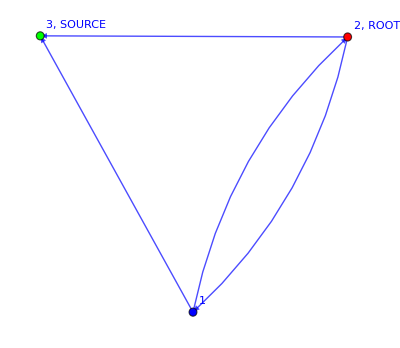
{-Graphics-,2,3}

-Graphics-

2

```mathematica
Clear[g,edges,β,root,source,printEdgesLabel]
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source,β]
g[[1]]
g[[2]]
```

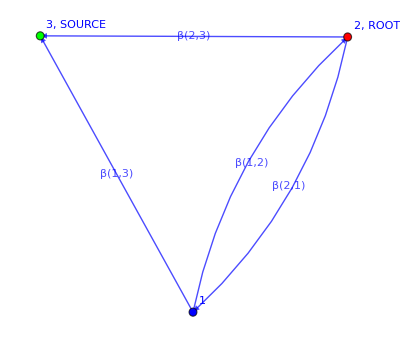

{EdgeLabels→{EdgeWeight},EdgeShapeFunction→{FilledArrow},EdgeStyle→{RGBColor[0, 0, 1]},VertexLabels→{Name,2→2, ROOT,3→3, SOURCE},VertexStyle→{RGBColor[0, 0, 1],3→RGBColor[0, 1, 0],2→RGBColor[1, 0, 0]},EdgeWeight→{β[1,2],β[2,1],β[2,3],β[1,3]}}

```mathematica
gLabel=MyGraph[edges,root,source,β,"printEdgesLabel"->True]
Options[gLabel]
```

## Vertex rules and VertexAssignment[]

The vertices are where the interaction takes place in the field theory.

```mathematica
Clear[V];
V[1]:=1;
V'[a_]:=1
```

```mathematica
Clear[VertexAssignment];
Options[VertexAssignment]={"system"->"LERW","print"->False,"excludedVertices"->{}};

VertexAssignment[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,x,y},
Clear[i];
locVertices=VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

(*LERW*)
If[OptionValue["system"]=="LERW",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,(1+ Sum[locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]]χ[x,Subscript[i, x]],{y,Length[locVertices]}] ) ],{x,Length[locVertices]}]
]];

(*DLA*)
If[OptionValue["system"]=="DLA",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,(1+ Product[1+locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]],{y,Length[locVertices]}] χ[x,Subscript[i, x]]+ Sum[locWeights[[x,y]]/totWeights[[x]] ϕs[y,Subscript[j, x]]ϕ[x,Subscript[j, x]],{y,Length[locVertices]}]) ],{x,Length[locVertices]}]
]]
]
```

### Usage example of VertexAssignment[]

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW"]
```

(1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3]))

```mathematica
VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{1}]
```

1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3])

## δrules

```mathematica
ClearAll[Σδrule]
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]):>δ[a,c],
δ[a_,a_]/;(!NumericQ[a]):>n};
```

```mathematica
ClearAll[δruleExternal]
δruleExternal={δ[a_,a_]/;(NumericQ[a]):>1,
δ[a_,b_]/;(NumericQ[a])/;(!a==b):>0 };
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

n

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

n

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

1

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

0

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

n

## WickContraction[]

NOW IT WORKS!!!

```mathematica
Clear[WickContraction];
(*/. 1+c_->κ+1+c*)
Options[WickContraction]={"print"->False};

WickContraction[A_ +B_]:=WickContraction[A]+WickContraction[B];
WickContraction[A_ +B_+C_]:=WickContraction[A]+WickContraction[B+C];

WickContraction[A_?NumericQ]:=A;

(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)
WickContraction[V[A_] *B_, OptionsPattern[]]:=Module[{contributions=0,z,zTemp,κ,j},
z=V[A]B;
contributions=z;

For[j=1,j<=100,j++,
(*First contribution*)
zTemp=z/.χ[j,a_]->0/.χs[j,b_]->0;
If[zTemp-z=!=0,
z+=zTemp;
];

(*Second contribution*)
zTemp=z/. χ[j,a_]->χ[j,a]+κ *δχ[j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
];

zTemp=z/. χs[j,a_]->χs[j,a]+κ *δχs[j,a];
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0;
If[OptionValue["print"],
Print["#### "<>ToString[j]<>" ####"];
Print[z]
]
];

z=Expand[z];
zTemp=z//.δχ[j,a_]*δχs[j,b_]/;(!NumericQ[a*b]):>δ[a,b];

If[zTemp-z=!=0,
If[OptionValue["print"],
Print["#### Contraction "<>ToString[j]<>" ####"];
Print[z=zTemp]
]
];
z=zTemp/.δχ[j,a_]->0/.δχs[j,b_]->0;

If[contributions-z=!=0,
contributions+=z;
];

z=contributions;
];

z=z/.χ[x_,a_]->0;
z=z/.χs[y_,b_]->0;
z=z//.Σδrule;
Return[z]
]

(*WickContraction[V[A_] ]:=Module[{z,zTemp,κ,j},
z=V[A];
For[j=1,j<=100,j++,
zTemp=z/. 1+c_->κ+1+c/.χ[j,a_]->χ[j,a]+κ δχ[j,a];
z=z/. 1+c_->κ+1+c;
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0];
z=z/.κ->0;

zTemp=z/. 1+c_->κ+1+c/.χs[j,a_]->χs[j,a]+κ δχs[j,a];
z=z/. 1+c_->κ+1+c;
If[zTemp-z=!=0,
z=D[zTemp,κ]/.κ->0];
z=z/.κ->0;

z=Expand[z];
z=z//.δχ[j,a_]*δχs[j,b_]/;(!NumericQ[a*b]):>δ[a,b];
];

z=z/.χ[x_,a_]->0;
z=z/.χs[y_,b_]->0;
z=z//.Σδrule;
Return[z]
]

WickContraction[A_ β[a_,b_]]:=A β[a,b];*)
```

### Usage example of WickContraction[]

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source,β];
Z=VertexAssignment[g[[1]],"system"->"LERW"]
WickContraction[Z]/.n->-1
```

(1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3]))

WickContraction[(1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,3]))]

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source,β];
g[[1]];
Z=VertexAssignment[g[[1]]]
WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,2] χ[2,i_2] χs[2,i_2])/(β[2,1]+β[2,2]+β[2,3])+(β[2,3] χ[2,i_2] χs[3,i_2])/(β[2,1]+β[2,2]+β[2,3])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,2]+β[2,3]))-β[2,2]/(β[2,1]+β[2,2]+β[2,3])

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source,β];
g[[1]];
Z=VertexAssignment[g[[1]]]

WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

We want to implement a partition function computing algorithm. LET’S TRY WITH THE STANDARD PRODUCT (i.e. commutation)

Throughout the code we use the Zeta function to replace positive parameters to avoid that Mathematica does weird stuff

After many trials, we arrived at the following conclusions:

1) In order to get the “loop structure”, we simply need the terms with the β_(...).

2) We do not need to explicate all the flavour indices: we just need to use different indices for each term, then use the Kronecker δ and then sum over them with the classical rules. When one obtains δ[a,a] then it’s equal to n. This number represents the number of fermions minus the number of bosons, and it is the “weight” of each loop. Kay says that we should substitute it with n->-2, but it seems that n->-1 is the one that works.

3) There is no need for any fancy commutation relation, berezinIntegral or wickContraction: simply use the nihilpotency of the fields to get rid of the “wrong” terms, then substitute:

```mathematica
ClearAll[nihilpotency]
nihilpotency=A_[x_,i_]*A_[x_,i_]->0;
```

```mathematica
ClearAll[contraction]
contraction={ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x],(*the Dδ reminds us the vertices of the loop*)
ϕ[x_,a_]*ϕs[y_,b_]->0}
```

{ϕ[x_,a_] ϕs[x_,b_]→Dδ[x] δ[a,b,x],ϕ[x_,a_] ϕs[y_,b_]→0}

4) Finally, simplify the δ’s and substitute everything

```mathematica
ClearAll[Σδrule]
Σδrule={δ[b_,a_]δ[c_,b_]/;(!NumericQ[b]):>δ[c,a],δ[a_,b_]δ[b_,c_]/;(!NumericQ[b]):>δ[a,c],δ[a_,a_]/;(!NumericQ[a]):>n};
```

```mathematica
ClearAll[ΣδruleMod]
ΣδruleMod={δ[b_,a_,x_]δ[c_,b_,y_]/;(!NumericQ[b]):>δ[c,a,y]Dδ[y,x],δ[a_,b_,x_]δ[b_,c_,y_]/;(!NumericQ[b]):>δ[a,c,x]Dδ[x,y],δ[a_,a_,x_]/;(!NumericQ[a]):>n};
```

```mathematica
ClearAll[ΣDδruleMod]
ΣDδruleMod={Dδ[a_]Dδ[a_,b_]Dδ[b_]->Dδ[a,b]Dδ[b],Dδ[a_,b_]Dδ[b_]Dδ[b_,c_]->Dδ[a,b]Dδ[b,c]};
```

```mathematica
%/.{n->-1,Dδ[a__]->1}
```

{1→1,1→1}

4.bis) If there are external fields (e.g. in correlators) then we do not want to sum over their indices. Instead we want to keep only the terms which yield a non-vanishing

```mathematica
ClearAll[δruleExternalMod]
δruleExternalMod={δ[a_,a_,x_]/;(NumericQ[a]):>1,δ[a_,b_,x_]/;(NumericQ[a])/;(!a==b):>0 };
```

```mathematica
ClearAll[δruleExternal]
δruleExternal={δ[a_,a_]/;(NumericQ[a]):>1,δ[a_,b_]/;(NumericQ[a])/;(!a==b):>0 };
```

E.g.1) Easiest case of all: simply 2 vertices: CORRECT!

```mathematica
(*From x*)(1+Zeta[5]/Zeta[3]ϕs[y,i]*ϕ[x,i])*
(*From y*)(1+Zeta[7]/Zeta[9]ϕs[x,j]*ϕ[y,j])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.ΣDδruleMod
%/.{Zeta[5]->Subscript[β, xy],Zeta[3]->Subscript[r, x],  Zeta[7]->Subscript[β, yx],Zeta[9]->Subscript[r, y]}
%/.{n->-1,Dδ[a__]->1}
```

1+(n Dδ[x] Dδ[y,x] Zeta[5] Zeta[7])/(Zeta[3] Zeta[9])

1+(n Dδ[x] Dδ[y,x] β_xy β_yx)/(r_x r_y)

1-(β_xy β_yx)/(r_x r_y)

E.g.2.1) Slightly more complicated: 3 vertices a,b,c. Starts from a and can go directly to c or passing through b. At b there can be a self-loop. Total absorption at c. CORRECT!!!!!

```mathematica
(*From a*)(1+Zeta[5]/Zeta[3]ϕs[c,i]*ϕ[a,i]+Zeta[7]/Zeta[3]ϕs[b,i]*ϕ[a,i])*
(*From b*)(1+Zeta[9]/Zeta[11]ϕs[c,j]*ϕ[b,j]+Zeta[15]/Zeta[11]ϕs[b,j]*ϕ[b,j])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.ΣDδruleMod
%/.{Zeta[5]->β'',Zeta[3]->Subscript[r, a],  Zeta[7]->β,Zeta[9]->β''',Zeta[13]->β,Zeta[11]->Subscript[r, b],Zeta[15]->β'}
Subscript[Z^d, abc]=%/.{n->-1,Dδ[a__]->1}
```

1+(n Dδ[b] Zeta[15])/Zeta[11]

1+(n Dδ[b] β')/r_b

1-β'/r_b

E.g.2.2) Slightly more complicated: 3 vertices a,b,c. Starts from a and can go directly to c or passing through b. At b there can be a self-loop and it could also come back to a. Total absorption at c. CORRECT!!!!!

```mathematica
(*From a*)(1+Zeta[5]/Zeta[3]ϕs[c,i]*ϕ[a,i]+Zeta[7]/Zeta[3]ϕs[b,i]*ϕ[a,i])*
(*From b*)(1+Zeta[9]/Zeta[11]ϕs[c,j]*ϕ[b,j]+Zeta[13]/Zeta[11]ϕs[a,j]*ϕ[b,j]+Zeta[15]/Zeta[11]ϕs[b,j]*ϕ[b,j])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b];
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.Σδrule;
%/.{Zeta[5]->β'',Zeta[3]->Subscript[r, a],  Zeta[7]->β,Zeta[9]->β''',Zeta[13]->β,Zeta[11]->Subscript[r, b],Zeta[15]->β'};
Subscript[Z^u, abc]=%/.{n->-1}
```

1-β^2/(r_a r_b)-β'/r_b

```mathematica
%/.{βs->1, β->1,βp->1,Subscript[r, b]->4,Subscript[r, a]->3}
```

11/12-(0&)/4

E.g.3.0) 2x2 square lattice: everything has the same weight and every vertex is connected both forward and backward. CORRECT!!!!!

```mathematica
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])*
(*From 1*)(1+Zeta[5]/Zeta[3]ϕs[0,l]*ϕ[1,l]+Zeta[5]/Zeta[3]ϕs[3,l]*ϕ[1,l])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.ΣDδruleMod;
%/.{Zeta[5]->β,Zeta[3]->r}
%/.{n->-1,Dδ[a__]->1}
```

1+(n β^2 Dδ[0] Dδ[1,0])/r^2+(n β^4 Dδ[2] Dδ[3] Dδ[0,2] Dδ[0,3] Dδ[1,0])/r^4+(n β^2 Dδ[3] Dδ[1,3])/r^2+(n β^2 Dδ[0] Dδ[2,0])/r^2+(n^2 β^4 Dδ[0] Dδ[3] Dδ[1,3] Dδ[2,0])/r^4+(n β^2 Dδ[2] Dδ[3,2])/r^2+(n^2 β^4 Dδ[0] Dδ[2] Dδ[1,0] Dδ[3,2])/r^4+(n β^4 Dδ[0] Dδ[1,3] Dδ[2,0] Dδ[3,2])/r^4

1-(4 β^2)/r^2

```mathematica
%/.{β->1,r->2}
```

0

E.g.3.1) 2x2 square lattice: same as before but 1 absorbs everything. CORRECT!!!!!

```mathematica
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.ΣDδruleMod;
%/.{Zeta[5]->β,Zeta[3]->r}
%/.{n->-1,Dδ[a__]->1}
```

1+(n β^2 Dδ[0] Dδ[2,0])/r^2+(n β^2 Dδ[2] Dδ[3,2])/r^2

1-(2 β^2)/r^2

```mathematica
%/.{β->1,r->2}
```

1/2

E.g.3.2) 2x2 square lattice: same as before but 1 absorbs only from 3. CORRECT!!!!!

```mathematica
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])*
(*From 1*)(1+Zeta[5]/Zeta[3]ϕs[0,l]*ϕ[1,l])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.ΣDδruleMod;
%/.{Zeta[5]->β,Zeta[3]->r}
%/.{n->-1,Dδ[a__]->1}
```

1+(n β^2 Dδ[0] Dδ[1,0])/r^2+(n β^2 Dδ[0] Dδ[2,0])/r^2+(n β^2 Dδ[2] Dδ[3,2])/r^2+(n^2 β^4 Dδ[0] Dδ[2] Dδ[1,0] Dδ[3,2])/r^4+(n β^4 Dδ[0] Dδ[1,3] Dδ[2,0] Dδ[3,2])/r^4

1-(3 β^2)/r^2

```mathematica
%/.{β->1,r->2}
```

1/4

We have checked many partition functions. Let’s now check the observable U(a,b,c)=sum of the probabilities of all LERWs going from a to c and passing through b. 			CORRECT!!!!

e.g.U1.1)Let’s begin with the most simple non-trivial example: that with the 3 vertices a b c with self-loop at b and total absorption at c. We then want to get the probability of a LERW passing through b. The observable is given by the correlator of 4 fields with fixed flavour indices.       CORRECT!!!!

```mathematica
ϕ[c,3]*ϕs[b,3]*ϕ[b,1]*ϕs[a,1](*From a*)(1+Zeta[5]/Zeta[3]ϕs[c,i]*ϕ[a,i]+Zeta[7]/Zeta[3]ϕs[b,i]*ϕ[a,i])*
(*From b*)(1+Zeta[9]/Zeta[11]ϕs[c,j]*ϕ[b,j]+Zeta[13]/Zeta[11]ϕs[a,j]*ϕ[b,j]+Zeta[15]/Zeta[11]ϕs[b,j]*ϕ[b,j])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.δruleExternal;
%//.ΣDδruleMod;
%/.{Zeta[5]->β'',Zeta[3]->Subscript[r, a],  Zeta[7]->β,Zeta[9]->β''',Zeta[13]->β,Zeta[11]->Subscript[r, b],Zeta[15]->β'};
%/.{n->-1,Dδ[a__]->1}
(*Now normalize it with 1/Z*)
%/Subscript[Z^u, abc]//FullSimplify
%/.{Subscript[r, b]->λ+β+β'+β''',Subscript[r, a]->λ+β+β''}//FullSimplify
%/.{β''->1, β->1,β'->1,β'''->1,λ->1}
```

(δ[1,3,b] δ[3,1,c] β' β'')/(r_a r_b)+(β δ[1,1,b] δ[3,3,c] β^(3))/(r_a r_b)

-(δ[1,3,b] δ[3,1,c] β' β''+β δ[1,1,b] δ[3,3,c] β^(3))/(β^2+r_a (-r_b+β'))

(δ[1,3,b] δ[3,1,c] β' β''+β δ[1,1,b] δ[3,3,c] β^(3))/(λ (2 β+λ)+(β+λ) β^(3)+β'' (β+λ+β^(3)))

1/8 (δ[1,3,b] δ[3,1,c]+δ[1,1,b] δ[3,3,c])

e.g. U1.2) Now let’s compute the one on the left. In order to do so we need a little trick: since we need a point through which the path goes, we add a fictitious extra vertex between a and c, which we’ll call b’. 		CORRECT!!!!

```mathematica
ϕ[c,2]*ϕs[b',2]*ϕ[b',1]*ϕs[a,1]*
(*From a*)(1+Zeta[5]/Zeta[3]ϕs[b',i]*ϕ[a,i]+Zeta[7]/Zeta[3]ϕs[b,i]*ϕ[a,i])*
(*From b*)(1+Zeta[9]/Zeta[11]ϕs[c,j]*ϕ[b,j]+Zeta[13]/Zeta[11]ϕs[a,j]*ϕ[b,j]+Zeta[15]/Zeta[11]ϕs[b,j]*ϕ[b,j])*
(*From b'*)(1+ϕs[c,k]ϕ[b',k])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b];
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.Σδrule;
%//.δruleExternal;
%/.{Zeta[5]->β'',Zeta[3]->Subscript[r, a],  Zeta[7]->β,Zeta[9]->β''',Zeta[13]->β,Zeta[11]->Subscript[r, b],Zeta[15]->β'};
%/.{n->-1};
(*Now normalize it with 1/Z*)
%/Subscript[Z^u, abc]//FullSimplify
```

-((r_b-β') β'')/(β^2+r_a (-r_b+β'))

```mathematica
%/.{Subscript[r, b]->λ+β+β'+β''',Subscript[r, a]->λ+β+β''}//FullSimplify
(*%/.{β''->1, β->1,β'->1,β'''->1,λ->1}*)
```

(β'' (β+λ+β^(3)))/(λ (2 β+λ)+(β+λ) β^(3)+β'' (β+λ+β^(3)))

e.g.U2.0) Now let’s try with something a little more complex: 2x2 square lattice with total absorption at 1.

Let’s start by defining the partition function: recall e.g.3.1

```mathematica
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.ΣDδruleMod;
%/.{Zeta[5]->β,Zeta[3]->r};
Z=%/.{n->-1,Dδ[a__]->1}
```

1-(2 β^2)/r^2

U2.1)Now define the observable U: let’s start with the probability to get the path 01. As in e.g. U1.1, we need the trick of an extra vertex between 0 and 1.		CORRECT!!!!!

```mathematica
ϕ[1,2]*ϕs[b',2]*ϕ[b',1]*ϕs[0,1](*From 0*)(1+Zeta[5]/Zeta[3]ϕs[b',i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])*
(*From b'*)(1+ϕs[1,l]*ϕ[b',l])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.δruleExternalMod;
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r};
%/.{n->-1,Dδ[a__]->1};
%/Z//FullSimplify
%/.{β->1,r->2}
```

((r-β) β (r+β))/(r^3-2 r β^2)

3/4

U2.2)Now define the observable U for the probability to get the path 0231. 		CORRECT!!!!!

```mathematica
ϕ[1,3]*ϕs[3,3]*ϕ[3,2]*ϕs[2,2]*ϕ[2,1]*ϕs[0,1]*
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[b',i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])*
(*From b'*)(1+ϕs[1,l]*ϕ[b',l])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.δruleExternal
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r};
%/.{n->-1,Dδ[a__]->1};
%/Z//FullSimplify
%/.{β->1,r->2}
```

(Dδ[0] Dδ[1] Dδ[2]^2 Dδ[3]^2 Dδ[b'] Dδ[1,0] Dδ[1,b'] Dδ[2,3] Dδ[3,2] Zeta[5]^3 δ[1,3,2] δ[2,2,3] δ[3,1,1])/Zeta[3]^3+(Dδ[0] Dδ[1] Dδ[2]^2 Dδ[3]^2 Dδ[1,3] Dδ[2,0] Dδ[3,2] Zeta[5]^3 δ[1,1,2] δ[2,2,3] δ[3,3,1])/Zeta[3]^3

(β^3 δ[2,2,3] (δ[1,3,2] δ[3,1,1]+δ[1,1,2] δ[3,3,1]))/(r^3-2 r β^2)

1/4 δ[2,2,3] (δ[1,3,2] δ[3,1,1]+δ[1,1,2] δ[3,3,1])

U2.3)Now define the observable U for the probability to get the path 231. 		CORRECT!!!!!

```mathematica
ϕ[1,3]*ϕs[3,3]*ϕ[3,2]*ϕs[2,2]*
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i]*ϕ[0,i]+Zeta[5]/Zeta[3]ϕs[2,i]*ϕ[0,i])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[0,j]*ϕ[2,j]+Zeta[5]/Zeta[3]ϕs[3,j]*ϕ[2,j])*
(*From 3*)(1+Zeta[5]/Zeta[3]ϕs[2,k]*ϕ[3,k]+Zeta[5]/Zeta[3]ϕs[1,k]*ϕ[3,k])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.δruleExternal;
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r};
%/.{n->-1,Dδ[a__]->1};
%/Z//FullSimplify
%/.{β->1,r->2}
```

(β^2 δ[2,2,3] δ[3,3,1])/(r^2-2 β^2)

1/2 δ[2,2,3] δ[3,3,1]

e.g.U3) Now even more complex: 3x3 square lattice with total absorption at 4 (the vertex in the center).

Let’s start by defining the partition function:

```mathematica
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i0]*ϕ[0,i0]+Zeta[5]/Zeta[3]ϕs[3,i0]*ϕ[0,i0])*
(*From 1*)(1+Zeta[5]/Zeta[7]ϕs[0,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[2,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[4,i1]*ϕ[1,i1])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[1,i2]*ϕ[2,i2]+Zeta[5]/Zeta[3]ϕs[5,i2]*ϕ[2,i2])*
(*From 3*)(1+Zeta[5]/Zeta[7]ϕs[0,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[4,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[6,i3]*ϕ[3,i3])*
(*From 5*)(1+Zeta[5]/Zeta[7]ϕs[2,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[4,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[8,i5]*ϕ[5,i5])*
(*From 6*)(1+Zeta[5]/Zeta[3]ϕs[3,i6]*ϕ[6,i6]+Zeta[5]/Zeta[3]ϕs[7,i6]*ϕ[6,i6])*
(*From 7*)(1+Zeta[5]/Zeta[7]ϕs[6,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[4,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[8,i7]*ϕ[7,i7])*
(*From 8*)(1+Zeta[5]/Zeta[3]ϕs[7,i8]*ϕ[8,i8]+Zeta[5]/Zeta[3]ϕs[5,i8]*ϕ[8,i8])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r2,Zeta[7]->r3};
Z=%/.{n->-1,Dδ[a__]->1}
```

1-(8 β^2)/(r2 r3)+(20 β^4)/(r2^2 r3^2)-(16 β^6)/(r2^3 r3^3)

```mathematica
Z
```

1-(8 β^2)/(r2 r3)+(20 β^4)/(r2^2 r3^2)-(16 β^6)/(r2^3 r3^3)

```mathematica
Z/.{β->1,r2->2,r3->3}
```

4/27

U3.1)Now define the observable U: let’s start with the probability to get the path 014. As in e.g. U1.1, we need the trick of an extra vertex between 0 and 1 and 1 and 4.		CORRECT!!!!! CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!

```mathematica
ϕ[4,4]*ϕs[c',4]*ϕ[c',3]*ϕs[1,3]*ϕ[1,2]*ϕs[b',2]*ϕ[b',1]*ϕs[0,1]*
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[b',i0]*ϕ[0,i0]+Zeta[5]/Zeta[3]ϕs[3,i0]*ϕ[0,i0])*
(*From 1*)(1+Zeta[5]/Zeta[7]ϕs[0,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[2,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[c',i1]*ϕ[1,i1])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[1,i2]*ϕ[2,i2]+Zeta[5]/Zeta[3]ϕs[5,i2]*ϕ[2,i2])*
(*From 3*)(1+Zeta[5]/Zeta[7]ϕs[0,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[4,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[6,i3]*ϕ[3,i3])*
(*From 5*)(1+Zeta[5]/Zeta[7]ϕs[2,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[4,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[8,i5]*ϕ[5,i5])*
(*From 6*)(1+Zeta[5]/Zeta[3]ϕs[3,i6]*ϕ[6,i6]+Zeta[5]/Zeta[3]ϕs[7,i6]*ϕ[6,i6])*
(*From 7*)(1+Zeta[5]/Zeta[7]ϕs[6,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[4,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[8,i7]*ϕ[7,i7])*
(*From 8*)(1+Zeta[5]/Zeta[3]ϕs[7,i8]*ϕ[8,i8]+Zeta[5]/Zeta[3]ϕs[5,i8]*ϕ[8,i8])*
(*From b'*)(1+ϕs[1,l]*ϕ[b',l])*
(*From c'*)(1+ϕs[4,i]*ϕ[c',i])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.Σδrule;
%//.δruleExternal;
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r2,Zeta[7]->r3};
%/.{n->-1,Dδ[a__]->1};
%/Z//FullSimplify
%/.{β->1,r2->2,r3->3}
```

(r2^3 r3^3 β^2-5 r2^2 r3^2 β^4+6 r2 r3 β^6-β^8)/(r2 r3 (r2 r3-4 β^2) (r2 r3-2 β^2)^2)

71/192

e.g.U4)  3x3 square lattice with total absorption at 8 (a vertex in the corner).

Let’s start by defining the partition function:

```mathematica
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[1,i0]*ϕ[0,i0]+Zeta[5]/Zeta[3]ϕs[3,i0]*ϕ[0,i0])*
(*From 1*)(1+Zeta[5]/Zeta[7]ϕs[0,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[2,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[4,i1]*ϕ[1,i1])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[1,i2]*ϕ[2,i2]+Zeta[5]/Zeta[3]ϕs[5,i2]*ϕ[2,i2])*
(*From 3*)(1+Zeta[5]/Zeta[7]ϕs[0,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[4,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[6,i3]*ϕ[3,i3])*
(*From 4*)(1+Zeta[5]/Zeta[9]ϕs[1,i4]*ϕ[4,i4]+Zeta[5]/Zeta[9]ϕs[3,i4]*ϕ[4,i4]+Zeta[5]/Zeta[9]ϕs[5,i4]*ϕ[4,i4]+Zeta[5]/Zeta[9]ϕs[7,i4]*ϕ[4,i4])*
(*From 5*)(1+Zeta[5]/Zeta[7]ϕs[2,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[4,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[8,i5]*ϕ[5,i5])*
(*From 6*)(1+Zeta[5]/Zeta[3]ϕs[3,i6]*ϕ[6,i6]+Zeta[5]/Zeta[3]ϕs[7,i6]*ϕ[6,i6])*
(*From 7*)(1+Zeta[5]/Zeta[7]ϕs[6,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[4,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[8,i7]*ϕ[7,i7])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]->δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r2,Zeta[7]->r3, Zeta[9]->r4};
Z=%/.{n->-1,Dδ[a__]->1}
```

1-(6 β^2)/(r2 r3)-(4 β^2)/(r3 r4)+(10 β^4)/(r2^2 r3^2)+(12 β^4)/(r2 r3^2 r4)-(4 β^6)/(r2^3 r3^3)-(8 β^6)/(r2^2 r3^3 r4)

```mathematica
Z%/.{β->1,r2->2,r3->3,r4->4}
```

4/729

U4.1)Now define the observable U: let’s start with the probability to get the path 01478. As in e.g. U1.1, we need the trick of an extra vertex between 0 and 1 and 1 and 4.		CORRECT!!!!! CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!CORRECT!!!!!

```mathematica
ϕ[7,4]*ϕs[c',5]*ϕ[7,5]*ϕs[c',5]*ϕ[c',4]*ϕs[4,4]*ϕ[4,3]*ϕs[b',3]*ϕ[b',2]*ϕs[1,2]*ϕ[1,1]*ϕs[0,1]*
(*From 0*)(1+Zeta[5]/Zeta[3]ϕs[b',i0]*ϕ[0,i0]+Zeta[5]/Zeta[3]ϕs[3,i0]*ϕ[0,i0])*
(*From 1*)(1+Zeta[5]/Zeta[7]ϕs[0,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[2,i1]*ϕ[1,i1]+Zeta[5]/Zeta[7]ϕs[c',i1]*ϕ[1,i1])*
(*From 2*)(1+Zeta[5]/Zeta[3]ϕs[1,i2]*ϕ[2,i2]+Zeta[5]/Zeta[3]ϕs[5,i2]*ϕ[2,i2])*
(*From 3*)(1+Zeta[5]/Zeta[7]ϕs[0,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[4,i3]*ϕ[3,i3]+Zeta[5]/Zeta[7]ϕs[6,i3]*ϕ[3,i3])*
(*From 5*)(1+Zeta[5]/Zeta[7]ϕs[2,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[4,i5]*ϕ[5,i5]+Zeta[5]/Zeta[7]ϕs[8,i5]*ϕ[5,i5])*
(*From 6*)(1+Zeta[5]/Zeta[3]ϕs[3,i6]*ϕ[6,i6]+Zeta[5]/Zeta[3]ϕs[7,i6]*ϕ[6,i6])*
(*From 7*)(1+Zeta[5]/Zeta[7]ϕs[6,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[4,i7]*ϕ[7,i7]+Zeta[5]/Zeta[7]ϕs[8,i7]*ϕ[7,i7])*
(*From 8*)(1+Zeta[5]/Zeta[3]ϕs[7,i8]*ϕ[8,i8]+Zeta[5]/Zeta[3]ϕs[5,i8]*ϕ[8,i8])*
(*From b'*)(1+ϕs[1,l]*ϕ[b',l])*
(*From c'*)(1+ϕs[4,i]*ϕ[c',i])(*single flavour contribution*)//Expand;
%/.nihilpotency;
%//.ϕ[x_,a_]*ϕs[x_,b_]/;(!NumericQ[a*b]):>δ[a,b,x]Dδ[x];(*the Dδ reminds us the vertices of the loop*)
%//.ϕ[x_,a_]*ϕs[y_,b_]->0;
%//.ΣδruleMod;
%//.δruleExternal;
(*%//.ΣDδruleMod;*)
%/.{Zeta[5]->β,Zeta[3]->r2,Zeta[7]->r3};
%/.{n->-1,Dδ[a__]->1};
%/Z//FullSimplify
%/.{β->1,r2->2,r3->3}
```

(r2^3 r3^3 β^2-5 r2^2 r3^2 β^4+6 r2 r3 β^6-β^8)/(r2 r3 (r2 r3-4 β^2) (r2 r3-2 β^2)^2)

71/192